```mathematica
(*raw = Import["~/Downloads/optimizerHistory_200um_0.30Best_noRF.json"];
(*raw = Import["/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"];*)*)

RadioButtonBar[
Dynamic[fileName],
{
"~/Downloads/optimizerHistory.json",
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json"
},Appearance->"Vertical"]

raw=Import[fileName];
```

| ~/Downloads/optimizerHistory.json
 | /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json

```mathematica
raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]
```

161

161

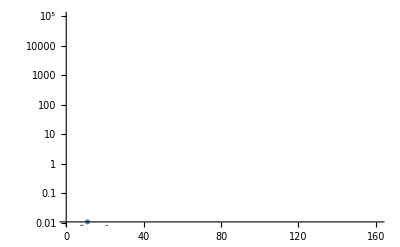

```mathematica
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{1*^5,All},
Joined->False
]
```

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]]
```

<|L1PhaseSet→-20.3858,L2PhaseSet→-37.9968,S1EL_xOffset→0.00334692,S1EL_yOffset→0.00100097,S2EL_xOffset→-0.000104198,S2EL_yOffset→0.000241114,S2ER_xOffset→-0.000116962,S2ER_yOffset→0.000999766,S1ER_xOffset→0.00398384,S1ER_yOffset→0.00176293,Q5FFkG→-89.949,Q4FFkG→-74.5112,Q3FFkG→98.0236,Q2FFkG→119.238,Q1FFkG→-231.625,Q0FFkG→141.144,XC1FFkG→0.355023,XC3FFkG→-0.187562,YC1FFkG→0.0104544,YC2FFkG→-0.0137555,PDrive_mean_x→2.7222×10^-6,PDrive_mean_y→-9.9645×10^-6,PDrive_sigma_x→0.0000486333,PDrive_sigma_y→0.0000389069,PDrive_mean_xp→0.000683227,PDrive_mean_yp→0.00018225,PDrive_median_x→-2.6032×10^-6,PDrive_median_y→5.919×10^-7,PDrive_median_xp→0.00072635,PDrive_median_yp→0.000177356,PDrive_sigmaSI90_x→0.0000335458,PDrive_sigmaSI90_y→0.0000354903,PDrive_emitSI90_x→0.0000698841,PDrive_emitSI90_y→0.0000340122,PDrive_zLen→0.0000201383,PDrive_zCentroid→991.332,PWitness_mean_x→2.6842×10^-6,PWitness_mean_y→4.135×10^-6,PWitness_sigma_x→0.0000269625,PWitness_sigma_y→0.0000228416,PWitness_mean_xp→0.000517375,PWitness_mean_yp→0.0000761791,PWitness_median_x→6.1976×10^-6,PWitness_median_y→3.3803×10^-6,PWitness_median_xp→0.000509957,PWitness_median_yp→0.0000754563,PWitness_sigmaSI90_x→0.0000237994,PWitness_sigmaSI90_y→0.0000211365,PWitness_emitSI90_x→0.0000211642,PWitness_emitSI90_y→5.0358×10^-6,PWitness_zLen→0.0000103979,PWitness_zCentroid→991.332,bunchSpacing→0.000159653,transverseCentroidOffset→0.0000140996,lostChargeFraction→0.,maximizeMe→0.0108555|>

```mathematica
(*Format for yml*)
string = ""
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
]
string
```

L1PhaseSet : -20.3857850146
L2PhaseSet : -37.9968468832
S1EL_xOffset : 0.0033469166
S1EL_yOffset : 0.0010009728
S2EL_xOffset : -0.0001041981
S2EL_yOffset : 0.000241114
S2ER_xOffset : -0.0001169616
S2ER_yOffset : 0.0009997657
S1ER_xOffset : 0.0039838381
S1ER_yOffset : 0.0017629304
Q5FFkG : -89.9490342122
Q4FFkG : -74.5111922076
Q3FFkG : 98.0236332553
Q2FFkG : 119.2379443218
Q1FFkG : -231.6254851445
Q0FFkG : 141.1441901631
XC1FFkG : 0.3550229518
XC3FFkG : -0.1875618337
YC1FFkG : 0.0104544394
YC2FFkG : -0.0137554991
PDrive_mean_x : 2.7222e-6
PDrive_mean_y : -9.9645e-6
PDrive_sigma_x : 0.0000486333
PDrive_sigma_y : 0.0000389069
PDrive_mean_xp : 0.000683227
PDrive_mean_yp : 0.0001822497
PDrive_median_x : -2.6032e-6
PDrive_median_y : 5.919e-7
PDrive_median_xp : 0.00072635
PDrive_median_yp : 0.0001773564
PDrive_sigmaSI90_x : 0.0000335458
PDrive_sigmaSI90_y : 0.0000354903
PDrive_emitSI90_x : 0.0000698841
PDrive_emitSI90_y : 0.0000340122
PDrive_zLen : 0.0000201383
PDrive_zCentroid : 991.3317198233
PWitness_mean_x : 2.6842e-6
PWitness_mean_y : 4.135e-6
PWitness_sigma_x : 0.0000269625
PWitness_sigma_y : 0.0000228416
PWitness_mean_xp : 0.000517375
PWitness_mean_yp : 0.0000761791
PWitness_median_x : 6.1976e-6
PWitness_median_y : 3.3803e-6
PWitness_median_xp : 0.0005099565
PWitness_median_yp : 0.0000754563
PWitness_sigmaSI90_x : 0.0000237994
PWitness_sigmaSI90_y : 0.0000211365
PWitness_emitSI90_x : 0.0000211642
PWitness_emitSI90_y : 5.0358e-6
PWitness_zLen : 0.0000103979
PWitness_zCentroid : 991.3318794765
bunchSpacing : 0.0001596532
transverseCentroidOffset : 0.0000140996
lostChargeFraction : 0.
maximizeMe : 0.0108554678

```mathematica
Norm[{bestCase["PDrive_mean_x"],bestCase["PDrive_mean_y"]}-{bestCase["PWitness_mean_x"],bestCase["PWitness_mean_y"]}]
```

0.0000140996

## Plot all

```mathematica
(*imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"L1PhaseSet","L2PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,Q0FFkG,Q1FFkG,Q2FFkG,Q3FFkG,Q4FFkG,Q5FFkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,XC1FFkG,XC3FFkG,YC1FFkG,YC2FFkG}

```mathematica
fitVar = "PDrive_zLen"
```

PDrive_zLen

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

FittedModel[…]

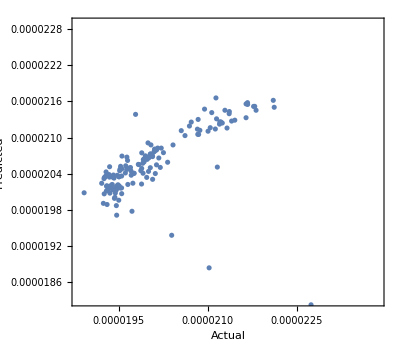

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

```mathematica
Minimize[
lm["BestFit"],
Symbol[#]&/@freeVarsMathematica
]
```

NMinimize::ubnd: The problem is unbounded.

{-∞,{L1PhaseSet→Indeterminate,L2PhaseSet→Indeterminate,Q0FFkG→Indeterminate,Q1FFkG→Indeterminate,Q2FFkG→Indeterminate,Q3FFkG→Indeterminate,Q4FFkG→Indeterminate,Q5FFkG→Indeterminate,S1ELxOffset→Indeterminate,S1ELyOffset→Indeterminate,S1ERxOffset→Indeterminate,S1ERyOffset→Indeterminate,S2ELxOffset→Indeterminate,S2ELyOffset→Indeterminate,S2ERxOffset→Indeterminate,S2ERyOffset→Indeterminate,XC1FFkG→Indeterminate,XC3FFkG→Indeterminate,YC1FFkG→Indeterminate,YC2FFkG→Indeterminate}}

*facepalm* It’s a linear model, obviously it’s unbounded

```mathematica
lm["ANOVATable"]
```

| DF | SS | MS | F-Statistic | P-Value
L1PhaseSet | 1 | 3.42737×10^-12 | 3.42737×10^-12 | 0.559681 | 0.455644
L2PhaseSet | 1 | 2.07934×10^-10 | 2.07934×10^-10 | 33.9551 | 3.71036×10^-8
Q0FFkG | 1 | 1.38405×10^-13 | 1.38405×10^-13 | 0.0226011 | 0.880715
Q1FFkG | 1 | 3.63989×10^-13 | 3.63989×10^-13 | 0.0594386 | 0.807742
Q2FFkG | 1 | 1.90722×10^-17 | 1.90722×10^-17 | 3.11445×10^-6 | 0.998594
Q3FFkG | 1 | 3.74166×10^-15 | 3.74166×10^-15 | 0.000611005 | 0.980315
Q4FFkG | 1 | 1.2337×10^-12 | 1.2337×10^-12 | 0.20146 | 0.654239
Q5FFkG | 1 | 6.41519×10^-13 | 6.41519×10^-13 | 0.104759 | 0.746675
S1ELxOffset | 1 | 1.18423×10^-12 | 1.18423×10^-12 | 0.193383 | 0.660794
S1ELyOffset | 1 | 7.86255×10^-17 | 7.86255×10^-17 | 0.0000128394 | 0.997146
S1ERxOffset | 1 | 7.47477×10^-17 | 7.47477×10^-17 | 0.0000122061 | 0.997217
S1ERyOffset | 1 | 1.58838×10^-14 | 1.58838×10^-14 | 0.00259378 | 0.959455
S2ELxOffset | 1 | 1.11887×10^-14 | 1.11887×10^-14 | 0.00182709 | 0.965966
S2ELyOffset | 1 | 8.87751×10^-15 | 8.87751×10^-15 | 0.00144968 | 0.969682
S2ERxOffset | 1 | 6.92464×10^-15 | 6.92464×10^-15 | 0.00113078 | 0.973222
S2ERyOffset | 1 | 1.37729×10^-15 | 1.37729×10^-15 | 0.000224908 | 0.988056
XC1FFkG | 1 | 4.61108×10^-13 | 4.61108×10^-13 | 0.0752979 | 0.784178
XC3FFkG | 1 | 5.10212×10^-14 | 5.10212×10^-14 | 0.00833164 | 0.927402
YC1FFkG | 1 | 8.61863×10^-17 | 8.61863×10^-17 | 0.000014074 | 0.997012
YC2FFkG | 1 | 1.08721×10^-14 | 1.08721×10^-14 | 0.00177539 | 0.966451
Error | 140 | 8.5733×10^-10 | 6.12379×10^-12 |  | 
Total | 160 | 1.07282×10^-9 |  |  |

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Plot::plld: Endpoints for x in {x,0.,0.} must have distinct machine-precision numerical values.

Show::gcomb: Could not combine the graphics objects in Show[,Plot[x,{x,Min[lm[Response]],Max[lm[Response]]},PlotStyle→Red]].

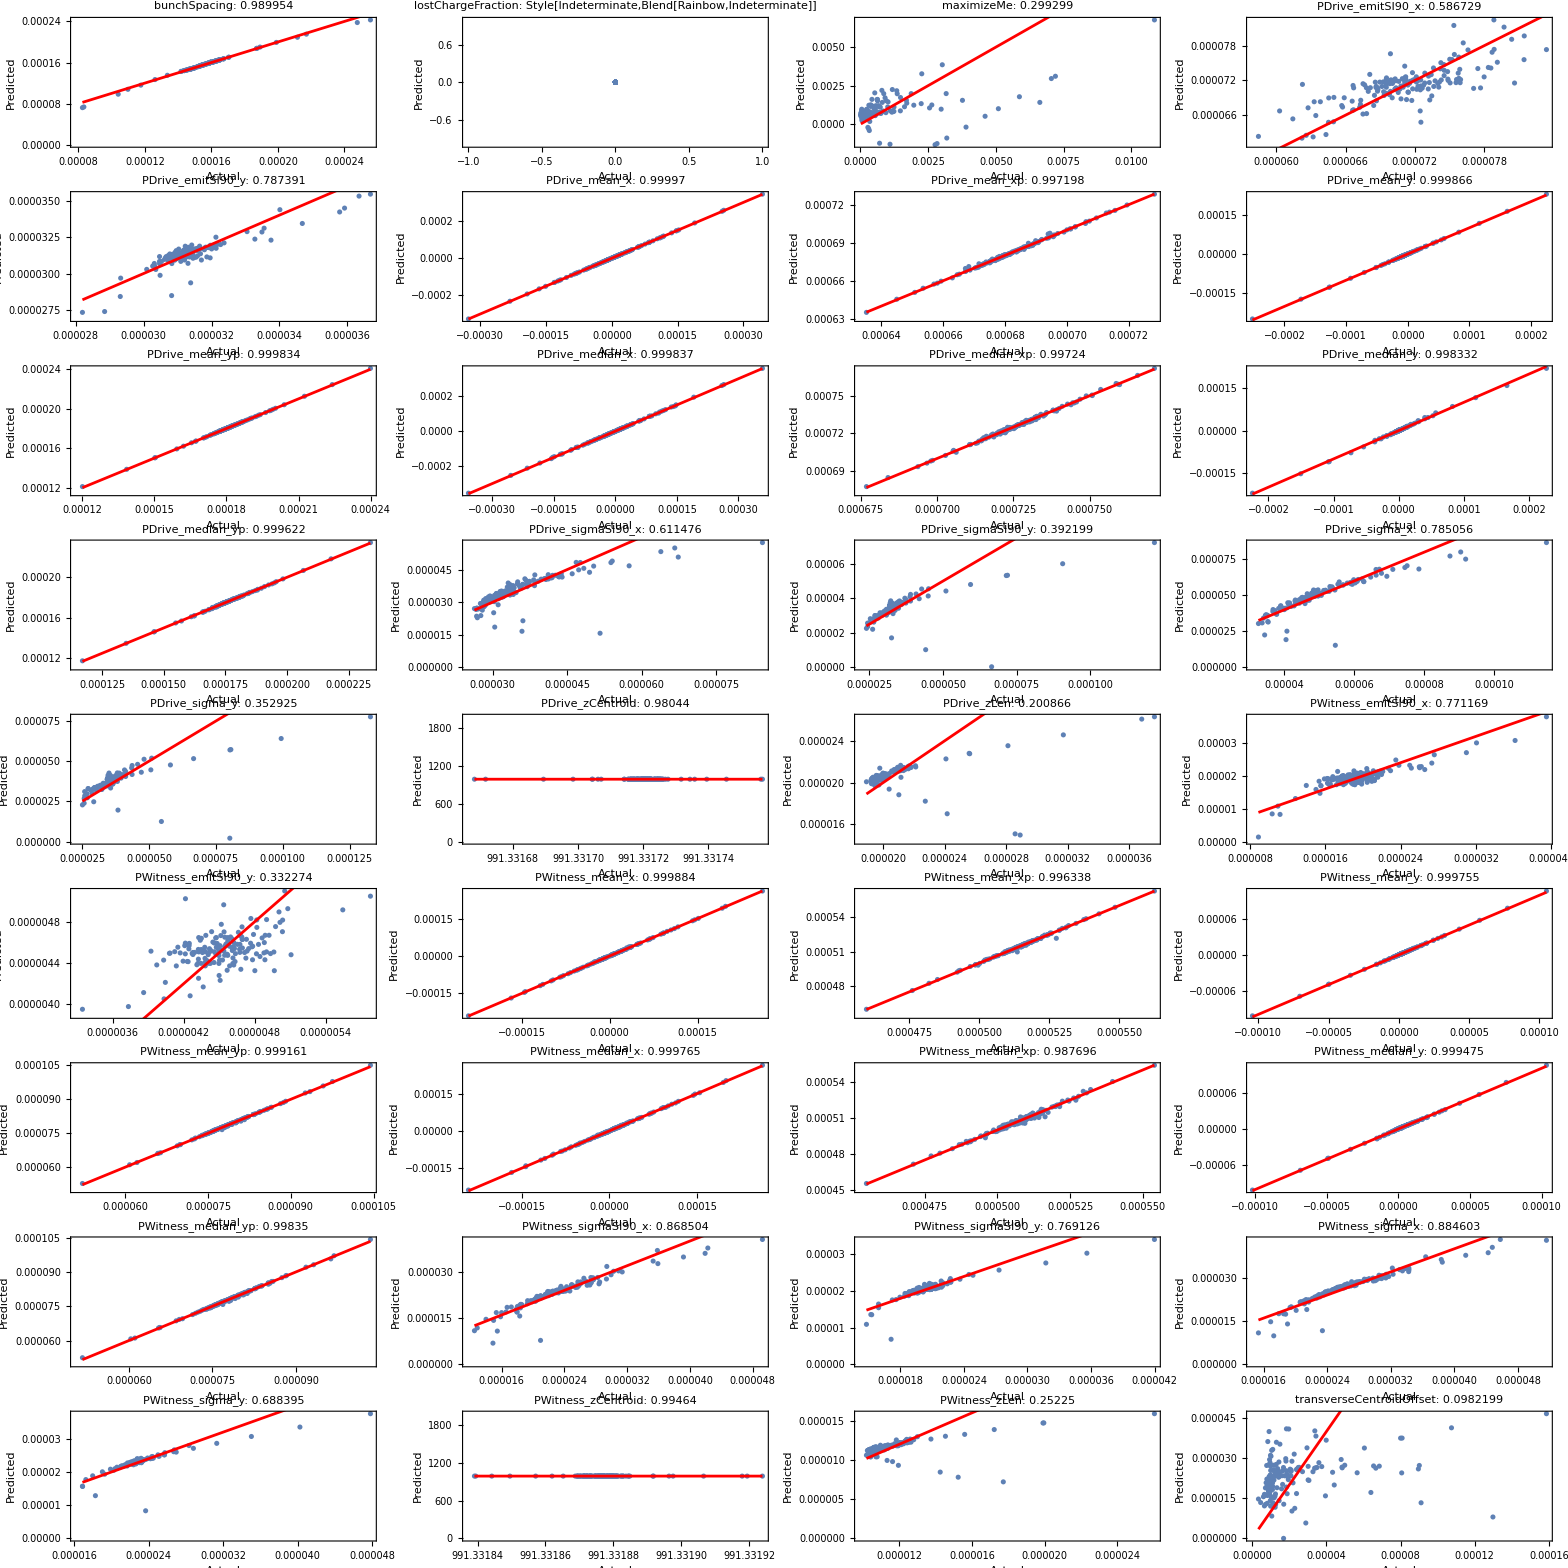

```mathematica
displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```